```mathematica
E1a[n_,k_, a_,s_]:= E1a[n,k,a,s]=Sum[j^(-s) E1a[n/j,k-1,a,s],{j,1,n}]-a Sum[(j a)^(-s) E1a[n/(a j),k-1,a,s],{j,1,n/a}];E1a[n_,0,a_,s_]:=1
DDa[n_,k_,s_]:=DDa[n,k,s]=Sum[j^(-s) DDa[Floor[n/j],k-1,s],{j,1,n}];DDa[n_,0,s_]:=1
DDc[n_,k_,b_,s_]:=Sum[Binomial[k+j-1,k-1] b^(j(1-s)) E1a[n/(b^j), k, b,s],{j,0,Log[b,n]}]
E1c[n_,k_,b_,s_]:=Sum[(-1)^j Binomial[k,j] b^(j(1-s))  DDa[n/b^j,k,s],{j,0,k}]
```

```mathematica
E1a[100,1,100,-1]
```

-4950

```mathematica
E1c[100,1,100,-1]
```

-4950

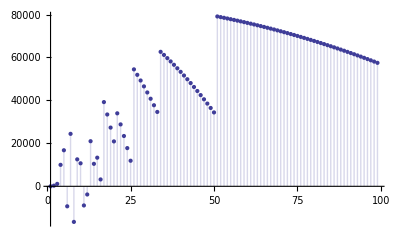

```mathematica
DiscretePlot[ E1a[100,3,n,-1],{n,1,99}]
```

```mathematica
DiscretePlot[E1c[100,3,n,-1],{n,1,99}]
```

-Graphics-

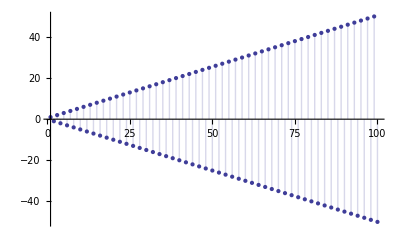

```mathematica
DiscretePlot[ E1a[n,1,2,-1],{n,1,100}]
```

```mathematica
DiscretePlot[ DDa[n,1,-1]-4 DDa[Floor[n/2],1,-1],{n,1,100}]
```

-Graphics-

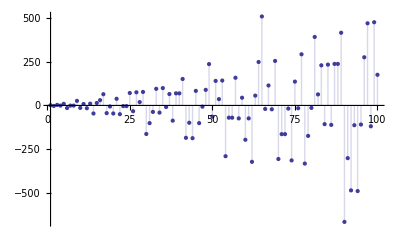

```mathematica
DiscretePlot[ E1a[n,2,2,-1],{n,1,100}]
```

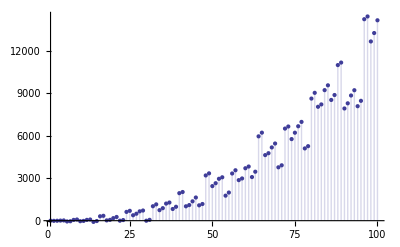

```mathematica
DiscretePlot[ ( DDa[n,2,-1]-16DDa[Floor[n/2],2,-1]+64 DDa[Floor[n/4],2,-1]),{n,1,100}]
```

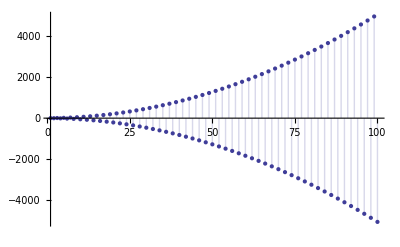

```mathematica
DiscretePlot[ E1a[n,1,2,-2],{n,1,100}]
```

```mathematica
DiscretePlot[ DDa[n,1,-2]-8 DDa[Floor[n/2],1,-2],{n,1,100}]
```

-Graphics-

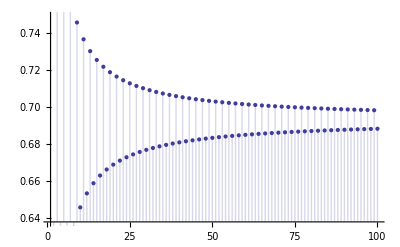

```mathematica
DiscretePlot[ E1a[n,1,2,1],{n,1,100}]
```

```mathematica
DiscretePlot[ DDa[n,1,1]-1 DDa[Floor[n/2],1,1],{n,1,100}]
```

-Graphics-

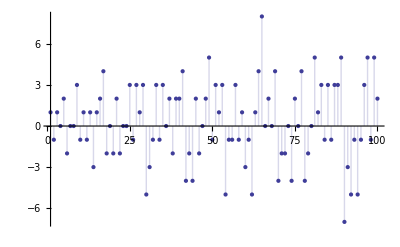

```mathematica
DiscretePlot[ E1a[n,2,2,0],{n,1,100}]
```

```mathematica
DiscretePlot[ ( DDa[n,2,0]-(2 2)DDa[Floor[n/2],2,0]+(1 4) DDa[Floor[n/4],2,0]),{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ E1a[n,2,2,-1],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ ( DDa[n,2,-1]-(2 2 2)DDa[Floor[n/2],2,-1]+(1 4 4) DDa[Floor[n/4],2,-1]),{n,1,100}]
```

-Graphics-

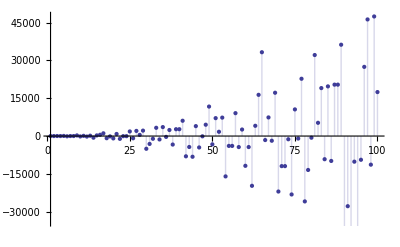

```mathematica
DiscretePlot[ E1a[n,2,2,-2],{n,1,100}]
```

```mathematica
DiscretePlot[ ( DDa[n,2,-2]-(2 2 4)DDa[Floor[n/2],2,-2]+(1 4 16) DDa[Floor[n/4],2,-2]),{n,1,100}]
```

-Graphics-

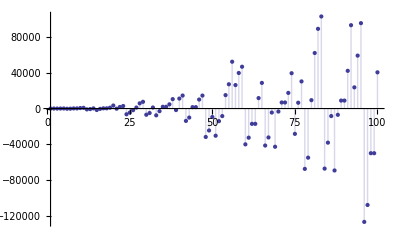

```mathematica
DiscretePlot[ E1a[n,2,3,-2],{n,1,100}]
```

```mathematica
DiscretePlot[ ( DDa[n,2,-2]-(2 3 9)DDa[Floor[n/3],2,-2]+(1 9 81) DDa[Floor[n/9],2,-2]),{n,1,100}]
```

-Graphics-

```mathematica
FullSimplify[b^j b^(-j s)]
```

b^(j-j s)

```mathematica
DDc[100,3,1.5,-1]
```

86914.

```mathematica
DDa[100,3,-1]
```

86914